```mathematica
(* Volume of the hiper-sphere: *)
(* Jacobian determinant. From https://en.wikipedia.org/wiki/N-sphere#Spherical_volume_and_area_elements *)
𝒥[d_]:=r^(d-1)∏_(k=1)^(d-1) Sin[Subscript[θ, k]]^(d-(k+1))
𝒥[1]
```

1

```mathematica
Integrate[1𝒥[1],{r,0,r}]
```

r

```mathematica
(* 2D: *)
𝒥[2]
```

r

```mathematica
Integrate[1𝒥[2], {ϕ,0,2π},{r,0,r}]
```

π r^2

```mathematica
(* 3D: *)
𝒥[3]
```

r^2 Sin[θ_1]

```mathematica
∫_0^(2π) ∫_0^π ∫_0^r 1𝒥[3] ⅆrⅆ Subscript[θ, 1]ⅆϕ
```

(4 π r^3)/3

```mathematica
Integrate[1𝒥[3],{Subscript[θ, 1],0,π},{ϕ,0,2π},{r,0,r}]
```

(4 π r^3)/3

```mathematica
(* 4D: *)
```

```mathematica
𝒥[4]
```

r^3 Sin[θ_1]^2 Sin[θ_2]

```mathematica
∫_0^(2π) ∫_0^π ∫_0^π ∫_0^r 1𝒥[4] ⅆrⅆ Subscript[θ, 1]ⅆ Subscript[θ, 2]ⅆϕ
```

(π^2 r^4)/2

```mathematica
Integrate[1𝒥[4],{Subscript[θ, 1],0,π},{Subscript[θ, 2],0,π},{ϕ,0,2π},{r,0,r}]
```

(π^2 r^4)/2

```mathematica
(* 5D: *)
𝒥[5]
```

r^4 Sin[θ_1]^3 Sin[θ_2]^2 Sin[θ_3]

```mathematica
∫_0^(2π) ∫_0^π ∫_0^π ∫_0^π ∫_0^r 1𝒥[5] ⅆrⅆ Subscript[θ, 1]ⅆ Subscript[θ, 2]ⅆ Subscript[θ, 3]ⅆϕ
```

(8 π^2 r^5)/15

```mathematica
(* All together: *)
Subscript[𝒱, d_][rr_]:= Integrate@@ FlattenAt[{r^(d-1)∏_(k=1)^(d-1) Sin[Subscript[θ, k]]^(d-(k+1)),Table[{Subscript[θ, k],0,π},{k,1,d-2}],{ϕ,0,If[d>1,2π,1]},{r,0,rr}},2]
```

```mathematica
Subscript[𝒱, 0][0]
```

0

```mathematica
Subscript[𝒱, 1][r]
```

r

```mathematica
Subscript[𝒱, 2][r]
```

π r^2

```mathematica
Subscript[𝒱, 3][r]
```

(4 π r^3)/3

```mathematica
Table[{d,Subscript[𝒱, d][r]}, {d, 1, 10}]//TableForm
```

1 | r
2 | π r^2
3 | (4 π r^3)/3
4 | (π^2 r^4)/2
5 | (8 π^2 r^5)/15
6 | (π^3 r^6)/6
7 | (16 π^3 r^7)/105
8 | (π^4 r^8)/24
9 | (32 π^4 r^9)/945
10 | (π^5 r^10)/120

```mathematica
Table[{d,Subscript[𝒱, d][1]}, {d, 2, 10}]
```

{{2,π},{3,(4 π)/3},{4,π^2/2},{5,(8 π^2)/15},{6,π^3/6},{7,(16 π^3)/105},{8,π^4/24},{9,(32 π^4)/945},{10,π^5/120}}

```mathematica
vs=Table[{d,Subscript[𝒱, d][1]}, {d, 2, 20}]//N
```

{{2.,3.14159},{3.,4.18879},{4.,4.9348},{5.,5.26379},{6.,5.16771},{7.,4.72477},{8.,4.05871},{9.,3.29851},{10.,2.55016},{11.,1.8841},{12.,1.33526},{13.,0.910629},{14.,0.599265},{15.,0.381443},{16.,0.235331},{17.,0.140981},{18.,0.0821459},{19.,0.0466216},{20.,0.0258069}}

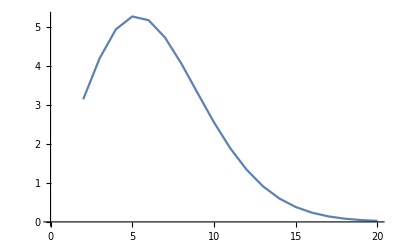

```mathematica
ListLinePlot[vs]
```

```mathematica
vs2=Table[{d,Subscript[𝒱, d][2]}, {d, 2, 20}]//N
```

{{2.,12.5664},{3.,33.5103},{4.,78.9568},{5.,168.441},{6.,330.734},{7.,604.77},{8.,1039.03},{9.,1688.84},{10.,2611.37},{11.,3858.64},{12.,5469.24},{13.,7459.87},{14.,9818.35},{15.,12499.1},{16.,15422.6},{17.,18478.7},{18.,21534.1},{19.,24443.1},{20.,27060.5}}

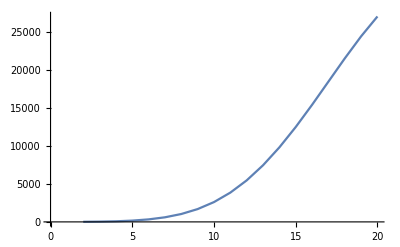

```mathematica
ListLinePlot[vs2]
```